As a aspiring fitness trainer it is my task to create training plans. When I attended a workshop called yoga in sport science, the tutor, which was a young golf teacher, created training plans in an excel sheet. Seeing that I thought there has to be a better way.
Today I want to demonstrate you how to create nice looking plans individually adapted with tons of possibilities from which I can show only a small excerpt, but still it will be for many too much too grasp, lets see.

There are two possibilities, for those who want to search for information just head over to [WolframAlpha](www.wolframalpha.com) and type yoga or pilates in the search field and will be welcomed with plenty of search examples, try them all out.
WolframAlpha is, unlike google, a semantic search engine which searches for information instead of links.

There is also a nifty overview [Health & Medicine]( www.wolframalpha.com/examples/science-and-technology/health-and-medicine/) site with examples for weight loss computations, heart rate calculators, body statistics, medical tests and computations, anatomy and so on. One can easily spend days there just to explore the possibilities.

For the adventurous ones of us, we dive even deeper and access the vast amount of information programmatically. If you want to follow along head over to the [Wolfram Cloud](https://develop.open.wolframcloud.com/app/), to access the Wolfram System notebook, an interactive interface for simple calculations to full publishable documents and sophisticated dynamic interfaces. If you want to save your changes you can further sign in, the free access has enough features for our needs. 

I will limit this tutorial to the YogaPose class, but you can as well check out the PilatesExercise class which has :

```mathematica
Length[EntityList["PilatesExercise"]]
53
```

exercise entities, which are more strength oriented like push ups and one leg kicks.

Now lets dive into the possibilities we have, the most obvious, the yoga poses:

```mathematica
EntityList["YogaPose"]
```

{Accomplished Pose,Ananta's Pose,Anjaneya's Pose,Archer Pose,Auspicious Pose,Balancing Half Moon Pose,Balancing Table Pose,Basic One-Legged King Pigeon Pose,Bharadvaja's Pose,Big Toe Pose,Bikram Triangle Pose,195,Upward Facing Dog Pose,Upward Facing Seated Forward Bend Pose,Upward Lotus Pose,Upward Plank Pose,Warrior III Pose,Warrior II Pose,Warrior I Pose,Wild Thing Pose,Wind Relieving Pose,Yoga Sleep Pose}
 |  |  |  |

Plenty to begin with, lets see how many we have, the % sign means use the last result:

```mathematica
Length[%]
216
```

Quite manageable i would say, lets see what else there is, how are they grouped?

```mathematica
EntityClassList["YogaPose"]
{EntityClass["YogaPose","ArmBalancingYogaPoses"],EntityClass["YogaPose","HeadStandingYogaPoses"],EntityClass["YogaPose","KneelingYogaPoses"],EntityClass["YogaPose","OneLeggedBalancingYogaPoses"],EntityClass["YogaPose","ProneYogaPoses"],EntityClass["YogaPose","QuadrupedYogaPoses"],EntityClass["YogaPose","RecliningYogaPoses"],EntityClass["YogaPose","SeatedYogaPoses"],EntityClass["YogaPose","ShoulderStandingYogaPoses"],EntityClass["YogaPose","StandingYogaPoses"],EntityClass["YogaPose","BackBendYogaPoses"],EntityClass["YogaPose","ForwardBendYogaPoses"],EntityClass["YogaPose","PosturalYogaPoses"],EntityClass["YogaPose","SideBendYogaPoses"],EntityClass["YogaPose","TwistYogaPoses"],EntityClass["YogaPose","InvertedYogaPoses"],EntityClass["YogaPose","BeginnerYogaPoses"],EntityClass["YogaPose","AdvancedYogaPoses"],EntityClass["YogaPose","IntermediateYogaPoses"],EntityClass["YogaPose","MediumIntensityYogaPoses"],EntityClass["YogaPose","HighIntensityYogaPoses"],EntityClass["YogaPose","LowIntensityYogaPoses"],EntityClass["YogaPose","YogaPosesToImproveBalance"],EntityClass["YogaPose","YogaPosesToImproveMobilityInAbdomen"],EntityClass["YogaPose","YogaPosesToImproveMobilityInAnkles"],EntityClass["YogaPose","YogaPosesToImproveMobilityInArms"],EntityClass["YogaPose","YogaPosesToImproveMobilityInBack"],EntityClass["YogaPose","YogaPosesToImproveMobilityInChest"],EntityClass["YogaPose","YogaPosesToImproveMobilityInFeet"],EntityClass["YogaPose","YogaPosesToImproveMobilityInHipJoints"],EntityClass["YogaPose","YogaPosesToImproveMobilityInLegs"],EntityClass["YogaPose","YogaPosesToImproveMobilityInNeck"],EntityClass["YogaPose","YogaPosesToImproveMobilityInKnees"],EntityClass["YogaPose","YogaPosesToImproveMobilityInButtocks"],EntityClass["YogaPose","YogaPosesToImproveMobilityInShoulders"],EntityClass["YogaPose","YogaPosesToImproveMobilityInThoracicVertebralColumn"],EntityClass["YogaPose","YogaPosesToImproveMobilityInVertebralColumn"],EntityClass["YogaPose","YogaPosesToImproveMobilityInWrists"],EntityClass["YogaPose","YogaPosesToImprovePosture"],EntityClass["YogaPose","YogaPosesToImproveStrengthInAbdomen"],EntityClass["YogaPose","YogaPosesToImproveStrengthInAnkles"],EntityClass["YogaPose","YogaPosesToImproveStrengthInArms"],EntityClass["YogaPose","YogaPosesToImproveStrengthInBack"],EntityClass["YogaPose","YogaPosesToImproveStrengthInChest"],EntityClass["YogaPose","YogaPosesToImproveStrengthInFeet"],EntityClass["YogaPose","YogaPosesToImproveStrengthInHands"],EntityClass["YogaPose","YogaPosesToImproveStrengthInHipJoints"],EntityClass["YogaPose","YogaPosesToImproveStrengthInLegs"],EntityClass["YogaPose","YogaPosesToImproveStrengthInKnees"],EntityClass["YogaPose","YogaPosesToImproveStrengthInNeck"],EntityClass["YogaPose","YogaPosesToImproveStrengthInButtocks"],EntityClass["YogaPose","YogaPosesToImproveStrengthInShoulders"],EntityClass["YogaPose","YogaPosesToImproveStrengthInWrists"],EntityClass["YogaPose","YogaPosesToStrengthenCalves"],EntityClass["YogaPose","YogaPosesToStrengthenDeepRotatorsOfHip"],EntityClass["YogaPose","YogaPosesToStrengthenGroin"],EntityClass["YogaPose","YogaPosesToStrengthenHamstrings"],EntityClass["YogaPose","YogaPosesToStrengthenHipFlexors"],EntityClass["YogaPose","YogaPosesToStrengthenIliopsoas"],EntityClass["YogaPose","YogaPosesToStrengthenPectoralMuscles"],EntityClass["YogaPose","YogaPosesToStrengthenPiriformis"],EntityClass["YogaPose","YogaPosesToStrengthenQuads"],EntityClass["YogaPose","YogaPosesToStrengthenRotatorCuff"],EntityClass["YogaPose","YogaPosesToStretchCalves"],EntityClass["YogaPose","YogaPosesToStretchDeepRotatorsOfHip"],EntityClass["YogaPose","YogaPosesToStretchGroin"],EntityClass["YogaPose","YogaPosesToStretchHamstrings"],EntityClass["YogaPose","YogaPosesToStretchHipFlexors"],EntityClass["YogaPose","YogaPosesToStretchIliopsoas"],EntityClass["YogaPose","YogaPosesToStretchPectoralisMinor"],EntityClass["YogaPose","YogaPosesToStretchPectoralMuscles"],EntityClass["YogaPose","YogaPosesToStretchPiriformis"],EntityClass["YogaPose","YogaPosesToStretchQuads"],EntityClass["YogaPose","YogaPosesToStretchRotatorCuff"]}
```

```mathematica
Length[%]
74
```

With that many categories there should be enough for every use case. But wait, there is more, we got various positions,

```mathematica
EntityList["YogaPosition"]
{Entity["YogaPosition","ArmBalancing"],Entity["YogaPosition","BackBend"],Entity["YogaPosition","ChinStanding"],Entity["YogaPosition","ForwardBend"],Entity["YogaPosition","HeadStanding"],Entity["YogaPosition","Kneeling"],Entity["YogaPosition","OneLeggedBalancing"],Entity["YogaPosition","Postural"],Entity["YogaPosition","Prone"],Entity["YogaPosition","Quadruped"],Entity["YogaPosition","Reclining"],Entity["YogaPosition","Seated"],Entity["YogaPosition","ShoulderStanding"],Entity["YogaPosition","SideBend"],Entity["YogaPosition","Standing"],Entity["YogaPosition","Twist"]}
```

properties ranging from Sanskrit names, props to use, counter poses, to which muscles are stretched or strengthened,

```mathematica
EntityProperties["YogaPose"]
{EntityProperty["YogaPose","AlternateNames"],EntityProperty["YogaPose","AssociatedPopularCurve"],EntityProperty["YogaPose","AssociatedSpecies"],EntityProperty["YogaPose","Asymmetrical"],EntityProperty["YogaPose","BodyPosition"],EntityProperty["YogaPose","Contraindications"],EntityProperty["YogaPose","CounterPoses"],EntityProperty["YogaPose","Description"],EntityProperty["YogaPose","ExperienceLevel"],EntityProperty["YogaPose","IntensityLevel"],EntityProperty["YogaPose","Inverted"],EntityProperty["YogaPose","JointMotion"],EntityProperty["YogaPose","Name"],EntityProperty["YogaPose","PotentialBenefits"],EntityProperty["YogaPose","Precautions"],EntityProperty["YogaPose","PreparatoryPoses"],EntityProperty["YogaPose","PrimaryContractedMuscles"],EntityProperty["YogaPose","Props"],EntityProperty["YogaPose","SanskritTransliteration"],EntityProperty["YogaPose","Schematic"],EntityProperty["YogaPose","SimplifiedSchematic"],EntityProperty["YogaPose","SitesOfImprovedFunction"],EntityProperty["YogaPose","SitesOfImprovedMobility"],EntityProperty["YogaPose","SitesOfImprovedStrength"],EntityProperty["YogaPose","SitesOfRecentSurgeryInjuryInflammation"],EntityProperty["YogaPose","SitesOfWeaknessStiffnessSensitivity"],EntityProperty["YogaPose","SpinePosition"],EntityProperty["YogaPose","StretchedMuscles"],EntityProperty["YogaPose","SupportingMuscles"],EntityProperty["YogaPose","TypicalSequences"],EntityProperty["YogaPose","Variations"]}
```

we can work with different sequences like the ashtanga primary or secondary series or the jivamukti spiritual warrior sequence,

```mathematica
EntityList["YogaSequence"]
{Entity["YogaSequence","AshtangaBackbendBeginner"],Entity["YogaSequence","AshtangaBackbendIntermediate"],Entity["YogaSequence","AshtangaClosingSequence"],Entity["YogaSequence","AshtangaPrimaryPart1"],Entity["YogaSequence","AshtangaPrimaryPart2"],Entity["YogaSequence","AshtangaPrimaryPart3"],Entity["YogaSequence","AshtangaPrimaryPart4"],Entity["YogaSequence","AshtangaPrimarySeries"],Entity["YogaSequence","AshtangaSecondPart1"],Entity["YogaSequence","AshtangaSecondPart2"],Entity["YogaSequence","AshtangaSecondPart3"],Entity["YogaSequence","AshtangaSecondPart4"],Entity["YogaSequence","AshtangaSecondSeries"],Entity["YogaSequence","AshtangaSevenHeadstands"],Entity["YogaSequence","AshtangaStandingSequence"],Entity["YogaSequence","BasicSunSalutation"],Entity["YogaSequence","BikramTwentySix"],Entity["YogaSequence","JivamuktiSpiritualWarrior"],Entity["YogaSequence","JivamuktiMagicTen"],Entity["YogaSequence","JivamuktiSunSalutationA"],Entity["YogaSequence","JumpBackVinyasa"],Entity["YogaSequence","JumpThroughVinyasa"],Entity["YogaSequence","SivanandaTwelveBasicPostures"],Entity["YogaSequence","SunSalutationA"],Entity["YogaSequence","SunSalutationB"],Entity["YogaSequence","Vinyasa"]}
```

## Example 1

Lets say my client wants wants to do just a few poses, which simultaneously strengthen their bootie, so obviously a female, strengthen her back, improve the mobility in her legs and strengthen her knees.

The orange boxes you see next are created through inline free-form input	fields which you can access with Ctrl+=.

You can then use free form linguistics to create the classes, like shown in bold, for example if you type "yoga poses to improve strength in back" and hit enter, you get the entity class EntityClass["YogaPose", "YogaPosesToImproveStrengthInBack"]. You can see the full class if you hover over them.

First we create 4 variables and store the poses of the different categories in it:

```mathematica
butt=EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInButtocks"]]
back=EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInBack"] ]
legs =EntityList[EntityClass["YogaPose","YogaPosesToImproveMobilityInLegs"]]
knees = EntityList[EntityClass["YogaPose","YogaPosesToImproveStrengthInKnees"]]
```

The Intersection command , which can also be typed as ∩ with ESC inter ESC, returns only the poses occurring in all 4 categories. 
If you see somewhere a variable in blue color it means that it is not evaluated yet, so head over to that cell and hit shift+enter.

```mathematica
finalplan=Intersection[butt, back, legs, knees]
{Entity["YogaPose","GoddessPose"],Entity["YogaPose","LordOfTheDancePose"],Entity["YogaPose","WarriorIIIPose"]}
```

There are just 3 poses matching all categories, lets see how they look like. 
The GraphicsRow command shows them without coma separated  list in parenthesis, when you want to copy the cell as image.

```mathematica
graph=GraphicsRow[EntityValue[finalplan,"SimplifiedSchematic"]]
```

-Graphics-

Maybe you don't like the color, how about pink?

```mathematica
graph /.RGBColor[___]->Pink
```

-Graphics-

You can resize them,

```mathematica
Show[pink,ImageSize ->Medium]
```

-Graphics-

or maybe you prefer the detailed schematics

```mathematica
EntityValue[finalplan,"Schematic"]
```

{-Graphics-,-Graphics-,-Graphics-}

## Example 2

You want to do poses which strengthen the most muscles at a time. The Property we need for that is called "sites of improved strength" in natural language. Because we work with properties instead of classes, we need to associate the poses with the muscles which will be strengthened. As we see in the shortened associative array below, the wind relieving pose is not in the group of poses that make you strong.

```mathematica
ev=EntityValue["YogaPose", 
  EntityProperty["YogaPose", "SitesOfImprovedStrength"], "EntityAssociation"]
```

Accomplished Pose→{back,abdomen},Ananta's Pose→{abdomen,back,hand,shoulder,leg},212,Wind Relieving Pose→Missing[NotAvailable],Yoga Sleep Pose→{abdomen,back,leg}
 |  |  |  |

Next we look how many entities we have that strengthen the most muscles in a nifty histogram:

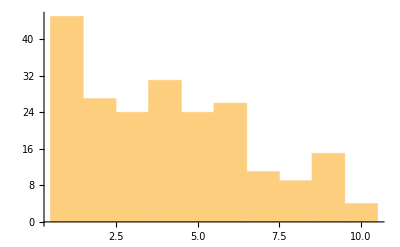

```mathematica
Histogram[Length /@ ev]
```

There are 4 poses which strengthen 10 muscles at the same time, lets see which ones.
We sort the list by the number of muscles involved, and give the -4 parameter to the Take command, which shows us the last 4 entries.

```mathematica
strength=Keys[Take[SortBy[ev, Length], -4]]
{Entity["YogaPose","ExtendedHandToBigToePoseB"],Entity["YogaPose","FireHydrantPose"],Entity["YogaPose","SidePlankPose"],Entity["YogaPose","WarriorIIIPose"]}
```

Lets pay a little respect to ancient India and get some Sanskrit names. I spared you the Devanagari script because the half letters are not joined. Fire hydrant pose has no name because there weren’t fire hydrants in ancient India, so i had to delete the Missing entry and  with the warrior III pose obviously not only human struggle, but the Keys command too, claiming that it is not a valid list of rules. The two names for this pose are vīrabhadrāsanaIII and digāsana.

```mathematica
sans=DeleteMissing[EntityValue[strength,"SanskritTransliteration"]]
Keys[sans[[{1,2}]]]
{{"utthita hasta pādāṅguṣṭhāsana B","utthita pārśvasahita"},{"vasiṣṭhāsana"}}
```

And here they are:

```mathematica
GraphicsRow[EntityValue[strength,EntityProperty["YogaPose", "SimplifiedSchematic"]] ,ImageSize ->Large]
```

-Graphics-

I hope I could give you a small glimpse of what is possible with the wolfram development platform, only the sky is the limit and your imagination is the limit.
Until next time,
Miron